```mathematica
L = 5
```

5

```mathematica
T = 240
```

240

```mathematica
U = 1
```

1

```mathematica
(* CP is 1/2 of base LP pool liquidity in millions of dollars *)
```

```mathematica
CP = 10
```

10

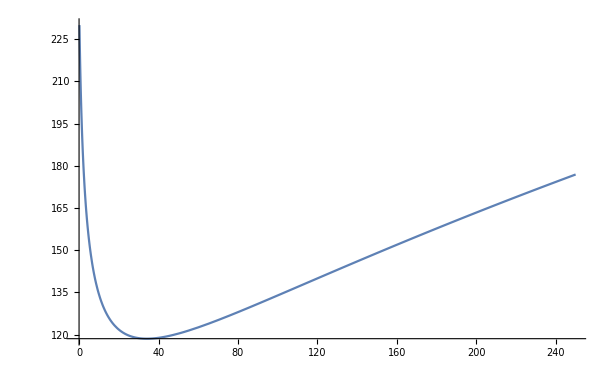

```mathematica
Plot[Piecewise[{{CP*(T/(L*Abs[x]) + U)*(1/Sqrt[1-Abs[x]] - 1),x<0},{CP*(T/(L*x) + U)*(Sqrt[1+x]-1),x>0}}],{x,-1,250}]
```

```mathematica
FindMinimum[CP*(T/(L*x) + U)*(Sqrt[1+x]-1),x]
```

{118.564,{x→34.1436}}

```mathematica
Show[%27,AxesLabel->{HoldForm[ϵ],HoldForm[TC]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%27,AxesLabel→{ϵ,TC},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

```mathematica
Export["/Users/personal/Desktop/tc_10m.svg",%30,"SVG"]
```

/Users/personal/Desktop/tc_10m.svg

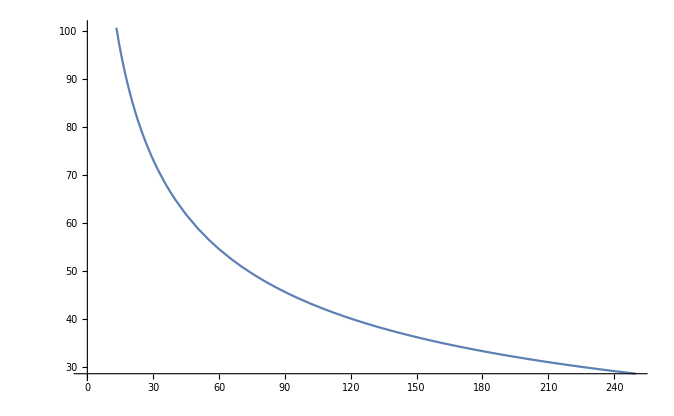

```mathematica
Plot[Piecewise[{{CP*(T/(L*Abs[x]))*(1/Sqrt[1-Abs[x]] - 1),x<0},{CP*(T/(L*x))*(Sqrt[1+x]-1),x>0}}],{x,-1,250}]
```

```mathematica
Show[%36,AxesLabel->{HoldForm[ϵ],HoldForm[N]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%36,AxesLabel→{ϵ,N},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

```mathematica
CP*(T/(L*34.14359353944894))*(Sqrt[1+34.14359353944894]-1)
```

69.282

```mathematica
(* Caps on OI can be made s.t. N break-even in [35] is not possible *)
```

```mathematica
(* What about taking advantage of TWAP as lagging metric? Bid/ask spread needs to be added *)
```

```mathematica
(* If using 1h TWAP, and know accumulator value right now, want to maximize probability bid/ask we offer is NOT profitable vs TWAP 1 hour into the future when value catches up to current spot price *)
```

```mathematica
(* Looking at B = P0 * e^{1/Δ * (X_t + F^{-1}_X(1-α))}, where X = Σ X_i *)
```

```mathematica
(* Examine for 1h TWAP on ETH/DAI. Distribution ... *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandle = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044,0.0015427669619594313]
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
edistWethUsdc90dFiltered1HourCandle = StableDistribution[1,1.597679462042982,-0.0971291600175433,-0.00015725436055898914,0.007900125269736371]
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
InverseCDF[edistWethUsdc90dFiltered1HourCandle , 0.999]
```

0.184654

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled1Hour = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044*6,0.0015427669619594313*(6)^(1/1.4646547203677354)]
```

StableDistribution[1,1.46465,-0.0496207,-0.0000633183,0.00524308]

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.999]
```

0.195974

```mathematica
(* Ok so close :) *)
```

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.999]]
```

1.0332

```mathematica
(* And if simply do 99% of time ... *)
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.99]
```

0.0424508

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.99]]
```

1.0071

```mathematica
(* Nice. Another 0.7% on top of the effect of the jump in price on twap at 99% confidence *)
```

```mathematica
(* And for 95% confidence? ... *)
```

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.95]]
```

1.00271

```mathematica
(* imagine a 5% jump in 10 min, what does that translate to in the twap? ... *)
```

```mathematica
x5pc10min = Log[1.05]
```

0.0487902

```mathematica
Exp[x5pc10min/6.0]
```

1.00816

```mathematica
(* Translates to 0.8% jump in twap. So buy/long price would be 1.5% greater than current TWAP price *)
```

```mathematica
(* and a 10% jump in 10 min ... *)
```

```mathematica
x10pc10min = Log[1.10]
```

0.0953102

```mathematica
Exp[x10pc10min/6.0]
```

1.01601

```mathematica
(* Translates to 1.6% jump in twap immediately. So buy/long price would be 2.3% greater than current twap price *)
```

```mathematica
Exp[1/6 * InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.9975]]
```

1.01776

```mathematica
(* Scale it down to 15s distribution *)
```

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.999975]/240]
```

1.01014

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled1Hour
```

StableDistribution[1,1.46465,-0.0496207,-0.0000633183,0.00524308]

```mathematica
0.005243083927982347/240.0
```

0.0000218462

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled1HourAveraged = StableDistribution[1, 1.4646547203677354, -0.04962071457296463, -0.00006331828389316227, 0.005243083927982347/240.0]
```

StableDistribution[1,1.46465,-0.0496207,-0.0000633183,0.0000218462]

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.99]
```

0.0424508

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1HourAveraged, 0.99]
```

0.000113824

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour, 0.99]/240.0
```

0.000176878

```mathematica
(* Seems weird and math looks off. Delta shouldnt impact what i'm getting as additional spread to use *)
```

```mathematica
(* I think I'm doing the sum calc wrong. Do it again ... *)
```

```mathematica
(* P1*P2*P3* ... *Pn = (P0)^{n} * e^{X_1} * e^{X_2} * e^{X_3} * ... * e^{X_n} = (P0)^{n} * e^{Σ X_i) *)
```

```mathematica
(* where X_i ~ S(a, b, i*mu*T, (iT)^{1/a} * sigma) ... ah yes. that's my problem :) *)
```

```mathematica
240*(241)/2.0
```

28920.

```mathematica
28920/240.0
```

120.5

```mathematica
(240*(241)/2.0)^(1/1.4)/240.0
```

6.40264

```mathematica
edistWethUsdc90dFiltered10MinCandle
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
6*7/2.0
```

21.

```mathematica
21^(1/1.4646547203677354)
```

7.99377

```mathematica
0.0015427669619594313*7.99376788340895
```

0.0123325

```mathematica
21 * -0.000010553047315527044
```

-0.000221614

```mathematica
XPrime10MinCandle = StableDistribution[1, 1.4646547203677354, -0.04962071457296463, -0.00022161399362606793, 0.012332520992095699]
```

StableDistribution[1,1.46465,-0.0496207,-0.000221614,0.0123325]

```mathematica
InverseCDF[XPrime10MinCandle, 0.99]
```

0.099778

```mathematica
Exp[InverseCDF[XPrime10MinCandle, 0.95]/6.0]
```

1.00639

```mathematica
Exp[InverseCDF[XPrime10MinCandle, 0.97]/6.0]
```

1.00854

```mathematica
(* 1.677% spread added to bid ends up covering 99% of cases after an hour. 0.639% covers 95%. 0.854% covers 97% ... i.e. 99% confident trader won't be profitable 1h into future given spread added to 1h TWAP buy price. *)
```

```mathematica
(* Use 15s candles ... *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled15Sec = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044/40.0,0.0015427669619594313*(1/40.0)^(1/1.4646547203677354)]
```

StableDistribution[1,1.46465,-0.0496207,-2.63826×10^-7,0.000124304]

```mathematica
(* For geometric mean, distribution in question has mu' = mu * Δ * (Δ + 1) / 2; σ' = σ * [Δ * (Δ + 1) / 2]^{1/a} *)
```

```mathematica
(* Assume 15s candles and 1h averaging window *)
```

```mathematica
ΔFactor[Δ_] := Δ * (Δ + 1) / 2.0
```

```mathematica
ΔFactor[240]
```

28920.

```mathematica
μGeometricTWAPScaled15Sec = -2.638261828881761*^-7 * ΔFactor[240]
```

-0.00762985

```mathematica
σGeometricTWAPScaled15Sec = 0.00012430432096353125 * ΔFactor[240] ^(1/1.4646547203677354)
```

0.138163

```mathematica
XPrime15SecCandle = StableDistribution[1, 1.4646547203677354, -0.04962071457296463,-0.007629853209126053,0.13816264757397648]
```

StableDistribution[1,1.46465,-0.0496207,-0.00762985,0.138163]

```mathematica
Exp[InverseCDF[XPrime15SecCandle, 0.99]/240.0]
```

1.00465

```mathematica
(* Beautiful... Compare with 10min candle XPrime ... *)
```

```mathematica
Exp[InverseCDF[XPrime10MinCandle, 0.99]/6.0]
```

1.01677

```mathematica
(* Hmm 10min candle XPrime has much higher 99% interval. Is this because of geometric mean? Or is my math off again. About 4x stricter with 10min candles *)
```

```mathematica
Exp[InverseCDF[XPrime15SecCandle, 0.999]/240.0]
```

1.02173

```mathematica
Exp[InverseCDF[XPrime10MinCandle, 0.999]/6.0]
```

1.07984

```mathematica
Exp[InverseCDF[XPrime15SecCandle, 0.995]/240.0]
```

1.00731

```mathematica
(* Around 0.7-1% spread is likely good... try with fits. If it's a geometric mean thing (avging) and my math isn't off, should use 15sec candle given blocks => 0.7% is at 99.5% confidence level *)
```

```mathematica
(* Look at 1h from now at 99% level as rough estimate: if jump gives P_t then do as ~ P_t * exp(spread_x) where spread_x = F_X^{-1}(1-alpha) *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled1Hour
```

StableDistribution[1,1.46465,-0.0496207,-0.0000633183,0.00524308]

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour,0.99]
```

0.0424508

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour,0.99]]
```

1.04336

```mathematica
(* Yea so 4% is too big of a spread ... *)
```

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour,0.95]]
```

1.0164

```mathematica
(* 1.64% not terrible but still rough *)
```

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour,0.90]]
```

1.01099

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandleScaled1Hour,0.85]]
```

1.00838

```mathematica
(* Geometric mean/averaging definitively dampens significantly. Is math off again? *)
```

```mathematica
(* ALSO: What's the goal w spread? Eliminate lag trade or eliminate lag trade + make it really hard to make money in the short term before funding has some time to kick in? *)
(* Former essentially addresses the TWAP only. Making it really hard to make money in short term (≤ 1h) tries to address participants who have more knowledge than the market - might not be best way to do it tho. *)
```

```mathematica
(* Instead, have 10min TWAP vs 1h TWAP. 10min TWAP acts as a proxy for spot. 1h TWAP guards against large manip moves like 34x changes. 10m TWAP guards guards against lag trade when acting as spot proxy AND guards against manip on the spot spread calc thru 10m avg. Trader when spot jumps can only manip the 10m TWAP back down to the 1h TWAP to lower spread *)
```

```mathematica
(* Tune the static spread such that 99%+ of the time, can't front-run the 10m and make a profit. What's inverse CDF over 10min candle? *)
```

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.95]]
```

1.00481

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.99]]
```

1.01258

```mathematica
(* Remember spread gets hit twice. Once on ask at build then again on bid at unwind *)
```

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.9925]]
```

1.01515

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.995]]
```

1.01979

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.999]]
```

1.05937

```mathematica
(* likely good with s = InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.99]/2 so 99% of time, we're fine *)
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.99]/2.0
```

0.00624957

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.99]/2.0]
```

1.00627

```mathematica
Exp[-InverseCDF[edistWethUsdc90dFiltered10MinCandle,0.99]/2.0]
```

0.99377

```mathematica
edistWethUsdc90dFiltered10MinCandle
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
(* What would it be for something closer to Cauchy? *)
```

```mathematica
eCauchyExample10MinCandle = StableDistribution[1, 1.0, 0.0, 0.0, 0.0015427669619594313]
```

StableDistribution[1,1.,0.,0.,0.00154277]

```mathematica
eCauchyExample10MinCandle
```

StableDistribution[1,1.,0.,0.,0.00154277]

```mathematica
Exp[InverseCDF[eCauchyExample10MinCandle , 0.99]/2.0]
```

1.02485

```mathematica
(* Interesting. Large spread, which is good *)
```

```mathematica
(* What about midway at around 1.2 alpha? *)
```

```mathematica
eMidExample10MinCandle = StableDistribution[1, 1.2, 0.0, 0.0, 0.0015427669619594313]
```

StableDistribution[1,1.2,0.,0.,0.00154277]

```mathematica
Exp[InverseCDF[eMidExample10MinCandle , 0.99]/2.0]
```

1.01254

```mathematica
(* Now, do out the math to be consistent/rigorous + think about market impact to be completely robust *)
```

```mathematica
(* Have an s. use per block fit to determine for 10m TWAP as spot proxy *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandleScaled15Sec
```

StableDistribution[1,1.46465,-0.0496207,-2.63826×10^-7,0.000124304]

```mathematica
mu  = -2.638261828881761*^-7
```

-2.63826×10^-7

```mathematica
a = 1.4646547203677354
```

1.46465

```mathematica
c = 0.00012430432096353125
```

0.000124304

```mathematica
sig = c * (a)^(1/a)
```

0.000161303

```mathematica
nu = 40
```

40

```mathematica
muSCalc = (mu/2) * (40-1)
```

-5.14461×10^-6

```mathematica
cSCalc = sig * (nu/a)^(1/a) * (1 - (1/nu)^a * (nu+1)/2)^(1/a)
```

0.00144404

```mathematica
edistSCalcWethUsdc90dFiltered10MinCandleScaled15Sec = StableDistribution[1, a, -0.04962071457296463, muSCalc, cSCalc]
```

StableDistribution[1,1.46465,-0.0496207,-5.14461×10^-6,0.00144404]

```mathematica
InverseCDF[edistSCalcWethUsdc90dFiltered10MinCandleScaled15Sec, 0.99]
```

0.011704

```mathematica
(* Beautiful. 99% gives around 1.2% spread on ask *)
```

```mathematica
InverseCDF[edistSCalcWethUsdc90dFiltered10MinCandleScaled15Sec, 0.95]
```

0.00449243

```mathematica
InverseCDF[edistSCalcWethUsdc90dFiltered10MinCandleScaled15Sec, 0.975]
```

0.00666762

```mathematica
InverseCDF[edistSCalcWethUsdc90dFiltered10MinCandleScaled15Sec, 0.97]
```

0.00599593

```mathematica
(* 97% gives around 0.6% of time 10m is worse. Consistent with samples from mc sims so far *)
```

```mathematica
(* Check consistent *)
```

```mathematica
mu/2 * (nu-1) + cSCalc * InverseCDF[StableDistribution[1, a, -0.04962071457296463, 0, 1],0.99]
```

0.011704

```mathematica
(* Perfect *)
```